```mathematica
ClearAll["Global`*"]
```

Path to the density profiles (“ density maps”)

```mathematica
PathMD="/Volumes/UNI/planar_densmaps_Version_v2/";
```

```mathematica
bulkLine=Line[{{-3,1000},{3,1000}}];
```

## SAM 0 %

## FIRST : we plot all density profiles to determine the (integration) interval where the water density has a stable bulk value. In order to do so we store the density values as lists in separate variables. For example (for the surface with 0% -OH coverage): WaterData0 and SurfData0 for mass densities (number densities not used anymore!!) We store the beginning and ending of each integration interval as start0 and end0 or start22 and end22 for example.

### Mass Density

Store water mass density of SAM 0 % in Waterdata0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData0 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 0 % in SurfData0

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam0_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData0 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

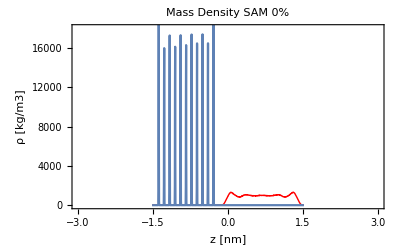

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Red,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True];
plot0=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

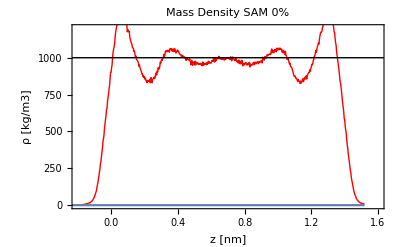

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Red,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True];
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Mass Density SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start0=0.308;
end0=1.059;
start0Line=Line[{{start0,0},{start0,1500}}];
end0Line=Line[{{end0,0},{end0,1500}}];
```

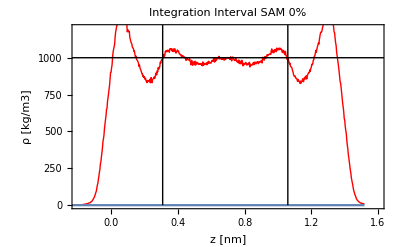

```mathematica
waterplot0=ListPlot[WaterData0,Joined->True,PlotStyle->{Red,Thick}];
surfplot0=ListPlot[SurfData0,Joined->True];
plot0zoom=Show[waterplot0,surfplot0,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start0Line,end0Line}]
```

## SAM 11 %

### Mass Density

Store water mass density of SAM 11 % in Waterdata11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData11 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 11 % in SurfData11

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam11_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData11 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

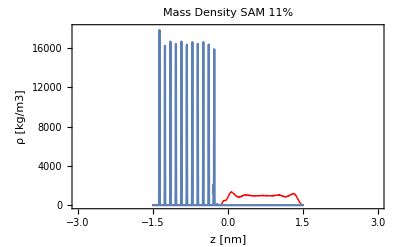

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

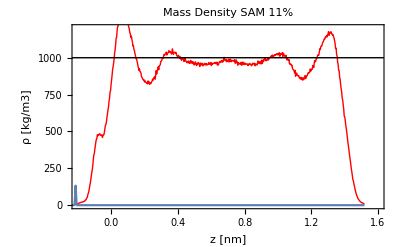

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Mass Density SAM 11%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start11=0.302;
end11=1.059;
start11Line=Line[{{start11,0},{start11,1500}}];
end11Line=Line[{{end11,0},{end11,1500}}];
```

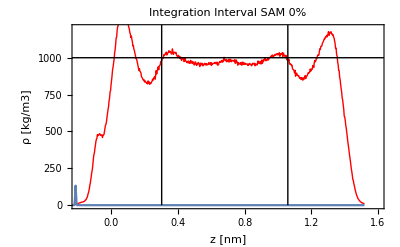

```mathematica
waterplot11=ListPlot[WaterData11,Joined->True,PlotStyle->{Red,Thick}];
surfplot11=ListPlot[SurfData11,Joined->True];
plot11zoom=Show[waterplot11,surfplot11,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start11Line,end11Line}]
```

## SAM 22 %

### Mass Density

Store water mass density of SAM 22 % in Waterdata22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData22 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 22 % in SurfData22

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam22_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData22 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

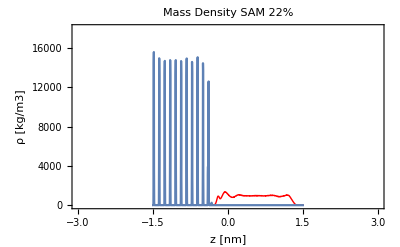

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

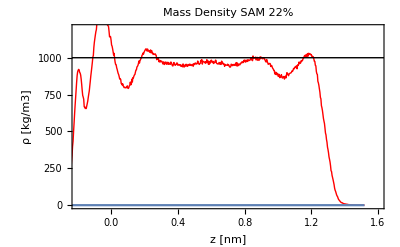

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Mass Density SAM 22%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start22=0.302;
end22=1.059;
start22Line=Line[{{start22,0},{start22,1500}}];
end22Line=Line[{{end22,0},{end22,1500}}];
```

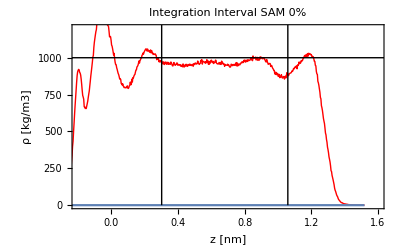

```mathematica
waterplot22=ListPlot[WaterData22,Joined->True,PlotStyle->{Red,Thick}];
surfplot22=ListPlot[SurfData22,Joined->True];
plot22zoom=Show[waterplot22,surfplot22,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start22Line,end22Line}]
```

## SAM 33 %

### Mass Density

Store water mass density of SAM 33 % in Waterdata33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData33 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 33 % in SurfData33

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam33_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData33 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

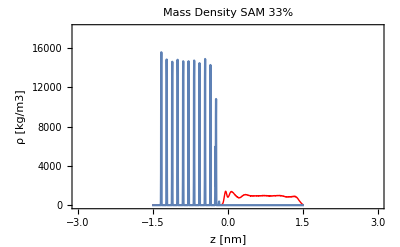

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

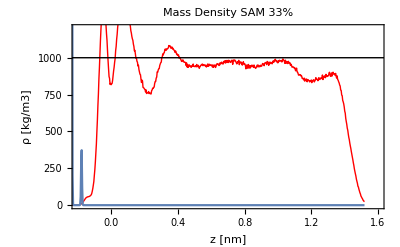

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Mass Density SAM 33%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start33=0.302;
end33=1.059;
start33Line=Line[{{start33,0},{start33,1500}}];
end33Line=Line[{{end33,0},{end33,1500}}];
```

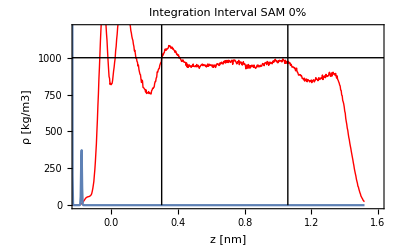

```mathematica
waterplot33=ListPlot[WaterData33,Joined->True,PlotStyle->{Red,Thick}];
surfplot33=ListPlot[SurfData33,Joined->True];
plot33zoom=Show[waterplot33,surfplot33,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start33Line,end33Line}]
```

## SAM 37 %

### Mass Density

Store water mass density of SAM 37 % in Waterdata37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData37 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 37 % in SurfData37

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam37_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData37 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

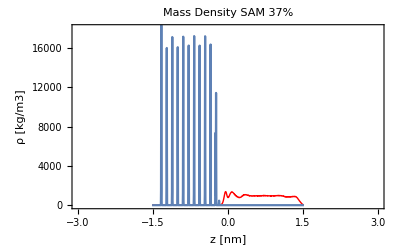

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

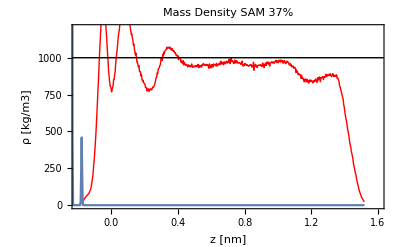

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Mass Density SAM 37%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start37=0.302;
end37=1.059;
start37Line=Line[{{start37,0},{start37,1500}}];
end37Line=Line[{{end37,0},{end37,1500}}];
```

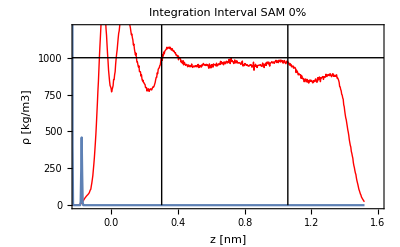

```mathematica
waterplot37=ListPlot[WaterData37,Joined->True,PlotStyle->{Red,Thick}];
surfplot37=ListPlot[SurfData37,Joined->True];
plot37zoom=Show[waterplot37,surfplot37,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start37Line,end37Line}]
```

## SAM 44 %

### Mass Density

Store water mass density of SAM 44 % in Waterdata44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_NVT_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","Water"},start=i],{i,1,Length[input]}];
WaterData44 = Take[input,{start+1,Length[input]}];
```

Store the surface mass density of SAM 44 % in SurfData44

```mathematica
(* Set file with density profile as input *)
input = Import[PathMD<>"dens_SAM_sam44_water_ptensor.xvg","Table"];
(* Extract data from file as list of 2D-vectors with the form: [z-position,density value] *)
Do[If[input[[i]] == {"@","s0","legend","non-Water"},start=i],{i,1,Length[input]}];
SurfData44 = Take[input,{start+1,Length[input]}];
```

Plot water and surface (mass) densities together

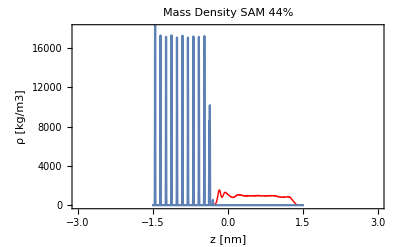

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-3,3.},{0,18000}}]
```

Zoom on bulk interval and add horizontal line at bulk value (1000 kg/m3) (“bulkLine” defined at beginning of notebook)

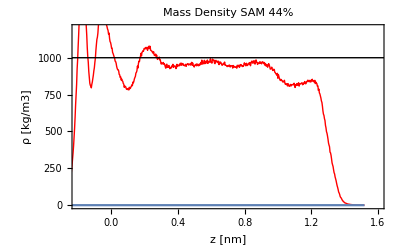

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Mass Density SAM 44%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}}, Epilog-> bulkLine]
```

Define beginning and ending positions of integration interval AND show as vertical lines on last density plot: 
- determine position of first intersection after first water peak (right-click to “get coordinates” manually) => store in start0
- determine position of last intersection before last water peak => store in end0
- make same plot again with vertical lines to “finetune” the values (and as a check)

```mathematica
start44=0.302;
end44=1.059;
start44Line=Line[{{start44,0},{start44,1500}}];
end44Line=Line[{{end44,0},{end44,1500}}];
```

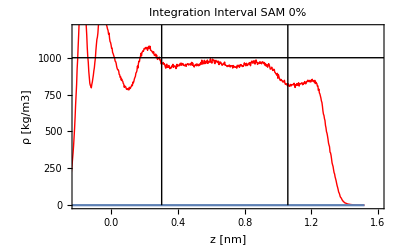

```mathematica
waterplot44=ListPlot[WaterData44,Joined->True,PlotStyle->{Red,Thick}];
surfplot44=ListPlot[SurfData44,Joined->True];
plot44zoom=Show[waterplot44,surfplot44,PlotLabel->"Integration Interval SAM 0%",FrameLabel->{"z [nm]","ρ [kg/m3]"},Frame->True,PlotRange->{{-0.2,1.6},{0,1200}},Epilog->{bulkLine,start44Line,end44Line}]
```